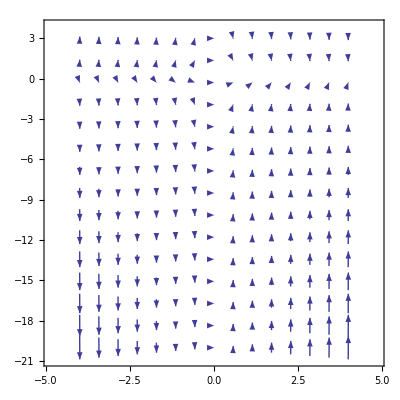

```mathematica
(* Vector Plot : dy/dx = -4xy *)
v1 = VectorPlot[{1, - 6 x y}, {x, -4, 4}, {y, -20, 3}]
```

```mathematica
d1 = DSolve[{y'[x] == -6 x y[x], y[0] == 7}, y[x], x]
```

{{y[x]→7 ⅇ^(-3 x^2)}}

```mathematica
d2 = DSolve[{y'[x] == -6 x y[x], y[2] == -4}, y[x], x]
```

{{y[x]→-4 ⅇ^(12-3 x^2)}}

```mathematica
d3 = DSolve[{y'[x] == -6 x y[x], y[1] == -4}, y[x], x]
```

{{y[x]→-4 ⅇ^(3-3 x^2)}}

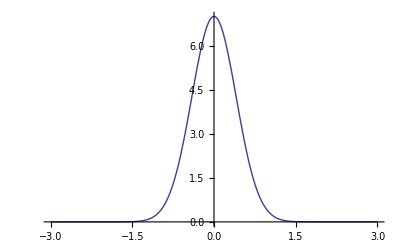

```mathematica
p1 = Plot[y[x]/.d1, {x, -3, 3}]
```

```mathematica
p2 = Plot[y[x]/.d2, {x, -3, 3}]
```

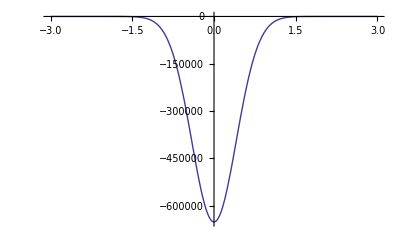

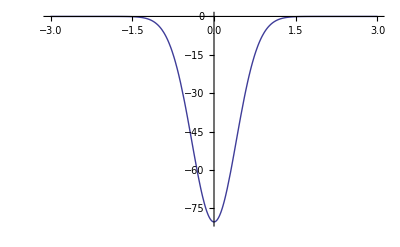

```mathematica
p3 = Plot[y[x]/.d3, {x, -3, 3}]
```

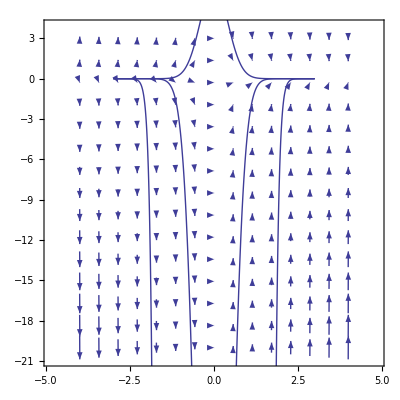

```mathematica
Show[v1, p1, p2, p3]
```

```mathematica
(*Vector Plot : dy/dx = 6 x(y-1)^(2/3)*)
v2 = VectorPlot[{1, 6*x *(y-1)^(2/3)}, {x, 0, 3}, {y, 0, 3}]
```

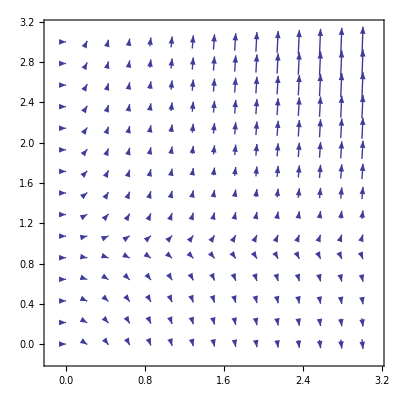

```mathematica
da1 = DSolve[{y'[x] == 6*x*(y[x]-1)^(2/3), y[1] == 1}, y[x], x]
```

{{y[x]→3 x^2-3 x^4+x^6}}

```mathematica
da2 = DSolve[{y'[x] == 6*x*(y[x]-1)^(2/3), y[0] == 1}, y[x], x]
```

{{y[x]→1+x^6}}

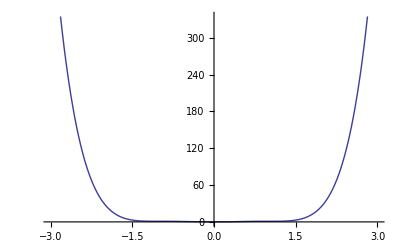

```mathematica
pa1 = Plot[y[x]/.da1, {x, -3, 3}]
```

```mathematica
pa2 = Plot[y[x]/.da2, {x, -5, 3}]
```

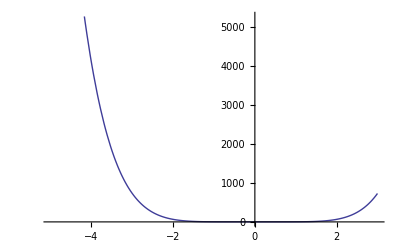

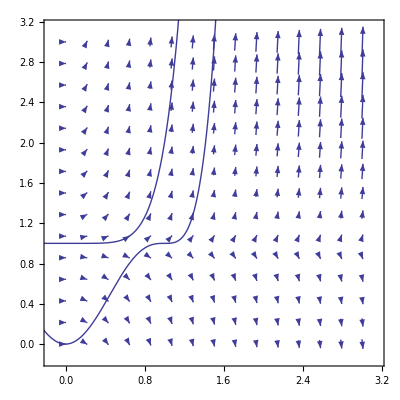

```mathematica
Show[v2, pa1, pa2]
```

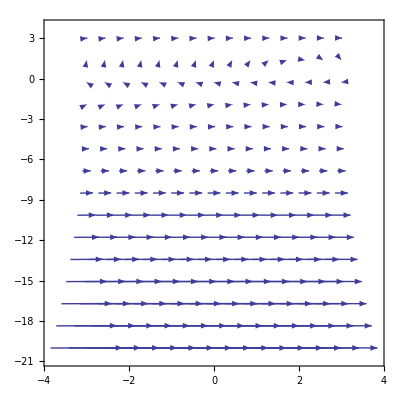

```mathematica
(* Vectorplot dy/dx=(4-2x)/(3y^2-5) *)
v3 = VectorPlot[{(3 y^2 - 5), (4 - 2 x)}, {x, -3, 3}, {y, -20, 3}]
```

```mathematica
db1 = DSolve[{y'[x] == (4 - 2x)/(3 y[x]^2 - 5), y[1] == 3}, y[x], x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→(10 2^(1/3) 3^(2/3)+2^(2/3) 3^(1/3) (81+36 x-9 x^2+√3 √(1687+1944 x-54 x^2-216 x^3+27 x^4))^(2/3))/(6 (81+36 x-9 x^2+√3 √(1687+1944 x-54 x^2-216 x^3+27 x^4))^(1/3))}}

```mathematica
db2 = DSolve[{y'[x] == (4 - 2x)/(3 y[x]^2 - 5), y[1] == 0}, y[x], x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→-(ⅈ (-30 2^(1/3) 3^(1/6)-10 ⅈ 2^(1/3) 3^(2/3)-ⅈ 2^(2/3) 3^(1/3) (-27+36 x-9 x^2+√3 √(-257-648 x+594 x^2-216 x^3+27 x^4))^(2/3)+2^(2/3) 3^(5/6) (-27+36 x-9 x^2+√3 √(-257-648 x+594 x^2-216 x^3+27 x^4))^(2/3)))/(12 (-27+36 x-9 x^2+√3 √(-257-648 x+594 x^2-216 x^3+27 x^4))^(1/3))}}

```mathematica
db3 = DSolve[{y'[x]==(4-2*x)/(3*(y[x])^2-5),y[1]==2},y[x],x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→(10 2^(1/3) 3^(2/3)+2^(2/3) 3^(1/3) (-45+36 x-9 x^2+√3 √(175-1080 x+702 x^2-216 x^3+27 x^4))^(2/3))/(6 (-45+36 x-9 x^2+√3 √(175-1080 x+702 x^2-216 x^3+27 x^4))^(1/3))}}

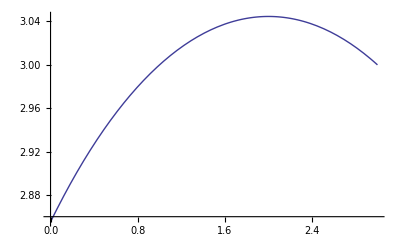

```mathematica
pb1 = Plot[y[x]/.db1, {x, 0, 3}]
```

```mathematica
pb2 = Plot[y[x]/.db2, {x, 0, 3}]
```

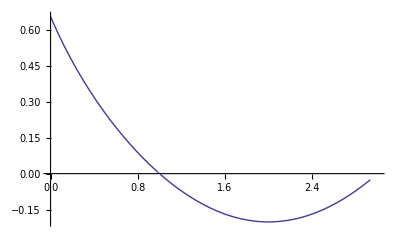

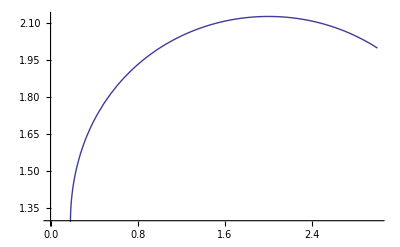

```mathematica
pb3 = Plot[y[x]/.db3, {x, 0, 3}]
```

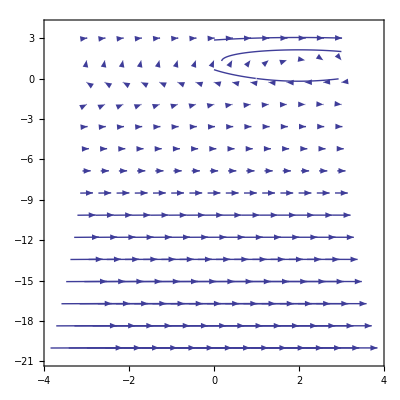

```mathematica
Show[v3, pb1, pb2, pb3]
```